```mathematica
SetDirectory[NotebookDirectory[]];Get["include/Perturbation_Theory.m"];Get["include/Pauli_Elem_Representation.m"];Get["include/Plotting_Definitions.m"];
```

```mathematica
(HJC0=( wc*DiagonalMatrix[{Subscript[n, 0]-0,Subscript[n, 0]-1,Subscript[n, 0]-1,Subscript[n, 0]-1,Subscript[n, 0]-1,Subscript[n, 0]-2,Subscript[n, 0]-2,Subscript[n, 0]-2,Subscript[n, 0]-2,Subscript[n, 0]-2,Subscript[n, 0]-2,Subscript[n, 0]-3,Subscript[n, 0]-3,Subscript[n, 0]-3,Subscript[n, 0]-3,Subscript[n, 0]-4}]+
DiagonalMatrix[{
E0L+E0R,
E0L+E1R,
E0L+E2R,
E1L+E0R,
E2L+E0R,
E0L+E3R,
E1L+E1R,
E1L+E2R,
E2L+E1R,
E2L+E2R,
E3L+E0R,
E1L+E3R,
E2L+E3R,
E3L+E1R,
E3L+E2R,
E3L+E3R
}]//.{E0L->0,E0R->0,E1L-> wffL,E1R-> wffR,E2L-> weL,E2R-> weR,E3L-> (wffL+weL),E3R-> (wffR+weR)}//.{wffL-> wc+δL,wffR-> wc+δR,weL-> wc+δeL,weR-> wc+δeR})-wc*Subscript[n, 0]* IdentityMatrix[16]//Simplify);
(HJCint=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {gffR*√Subscript[n, 0], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {geR*√Subscript[n, 0], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {gffL*√Subscript[n, 0], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {geL*√Subscript[n, 0], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, geR*√(Subscript[n, 0]-1), gffR*√(Subscript[n, 0]-1), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, gffL*√(Subscript[n, 0]-1), 0, gffR*√(Subscript[n, 0]-1), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, gffL*√(Subscript[n, 0]-1), geR*√(Subscript[n, 0]-1), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, geL*√(Subscript[n, 0]-1), 0, 0, gffR*√(Subscript[n, 0]-1), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, geL*√(Subscript[n, 0]-1), 0, geR*√(Subscript[n, 0]-1), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, geL*√(Subscript[n, 0]-1), gffL*√(Subscript[n, 0]-1), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, gffL*√(Subscript[n, 0]-2), geR*√(Subscript[n, 0]-2), gffR*√(Subscript[n, 0]-2), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, geL*√(Subscript[n, 0]-2), 0, 0, geR*√(Subscript[n, 0]-2), gffR*√(Subscript[n, 0]-2), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, geL*√(Subscript[n, 0]-2), 0, gffL*√(Subscript[n, 0]-2), 0, gffR*√(Subscript[n, 0]-2), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, geL*√(Subscript[n, 0]-2), 0, gffL*√(Subscript[n, 0]-2), geR*√(Subscript[n, 0]-2), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, geL*√(Subscript[n, 0]-3), gffL*√(Subscript[n, 0]-3), geR*√(Subscript[n, 0]-3), gffR*√(Subscript[n, 0]-3), 0}}));
(HJC=HJC0+HJCint+Transpose[HJCint])//MatrixForm
```

(0 | gffR √n_0 | geR √n_0 | gffL √n_0 | geL √n_0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gffR √n_0 | δR | 0 | 0 | 0 | geR √(n_0-1) | gffL √(n_0-1) | 0 | geL √(n_0-1) | 0 | 0 | 0 | 0 | 0 | 0 | 0
geR √n_0 | 0 | δeR | 0 | 0 | gffR √(n_0-1) | 0 | gffL √(n_0-1) | 0 | geL √(n_0-1) | 0 | 0 | 0 | 0 | 0 | 0
gffL √n_0 | 0 | 0 | δL | 0 | 0 | gffR √(n_0-1) | geR √(n_0-1) | 0 | 0 | geL √(n_0-1) | 0 | 0 | 0 | 0 | 0
geL √n_0 | 0 | 0 | 0 | δeL | 0 | 0 | 0 | gffR √(n_0-1) | geR √(n_0-1) | gffL √(n_0-1) | 0 | 0 | 0 | 0 | 0
0 | geR √(n_0-1) | gffR √(n_0-1) | 0 | 0 | δeR+δR | 0 | 0 | 0 | 0 | 0 | gffL √(n_0-2) | geL √(n_0-2) | 0 | 0 | 0
0 | gffL √(n_0-1) | 0 | gffR √(n_0-1) | 0 | 0 | δL+δR | 0 | 0 | 0 | 0 | geR √(n_0-2) | 0 | geL √(n_0-2) | 0 | 0
0 | 0 | gffL √(n_0-1) | geR √(n_0-1) | 0 | 0 | 0 | δeR+δL | 0 | 0 | 0 | gffR √(n_0-2) | 0 | 0 | geL √(n_0-2) | 0
0 | geL √(n_0-1) | 0 | 0 | gffR √(n_0-1) | 0 | 0 | 0 | δeL+δR | 0 | 0 | 0 | geR √(n_0-2) | gffL √(n_0-2) | 0 | 0
0 | 0 | geL √(n_0-1) | 0 | geR √(n_0-1) | 0 | 0 | 0 | 0 | δeL+δeR | 0 | 0 | gffR √(n_0-2) | 0 | gffL √(n_0-2) | 0
0 | 0 | 0 | geL √(n_0-1) | gffL √(n_0-1) | 0 | 0 | 0 | 0 | 0 | δeL+δL | 0 | 0 | gffR √(n_0-2) | geR √(n_0-2) | 0
0 | 0 | 0 | 0 | 0 | gffL √(n_0-2) | geR √(n_0-2) | gffR √(n_0-2) | 0 | 0 | 0 | δeR+δL+δR | 0 | 0 | 0 | geL √(n_0-3)
0 | 0 | 0 | 0 | 0 | geL √(n_0-2) | 0 | 0 | geR √(n_0-2) | gffR √(n_0-2) | 0 | 0 | δeL+δeR+δR | 0 | 0 | gffL √(n_0-3)
0 | 0 | 0 | 0 | 0 | 0 | geL √(n_0-2) | 0 | gffL √(n_0-2) | 0 | gffR √(n_0-2) | 0 | 0 | δeL+δL+δR | 0 | geR √(n_0-3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | geL √(n_0-2) | 0 | gffL √(n_0-2) | geR √(n_0-2) | 0 | 0 | 0 | δeL+δeR+δL | gffR √(n_0-3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | geL √(n_0-3) | gffL √(n_0-3) | geR √(n_0-3) | gffR √(n_0-3) | δeL+δeR+δL+δR)

```mathematica
DesiredStates={1,2,4,7,3,5};
RemainingStates=Complement[Table[i,{i,1,16}],DesiredStates];
```

```mathematica
(HJCReordered=HJC[[Join[DesiredStates,RemainingStates],Join[DesiredStates,RemainingStates]]]//.{δeL-> δe,δeR-> δe,δL->δ,δR->δ,gffL->gff,gffR->gff ,geL->ge,geR->ge })//MatrixForm
```

(0 | gff √n_0 | gff √n_0 | 0 | ge √n_0 | ge √n_0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gff √n_0 | δ | 0 | gff √(n_0-1) | 0 | 0 | ge √(n_0-1) | 0 | ge √(n_0-1) | 0 | 0 | 0 | 0 | 0 | 0 | 0
gff √n_0 | 0 | δ | gff √(n_0-1) | 0 | 0 | 0 | ge √(n_0-1) | 0 | 0 | ge √(n_0-1) | 0 | 0 | 0 | 0 | 0
0 | gff √(n_0-1) | gff √(n_0-1) | 2 δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ge √(n_0-2) | 0 | ge √(n_0-2) | 0 | 0
ge √n_0 | 0 | 0 | 0 | δe | 0 | gff √(n_0-1) | gff √(n_0-1) | 0 | ge √(n_0-1) | 0 | 0 | 0 | 0 | 0 | 0
ge √n_0 | 0 | 0 | 0 | 0 | δe | 0 | 0 | gff √(n_0-1) | ge √(n_0-1) | gff √(n_0-1) | 0 | 0 | 0 | 0 | 0
0 | ge √(n_0-1) | 0 | 0 | gff √(n_0-1) | 0 | δ+δe | 0 | 0 | 0 | 0 | gff √(n_0-2) | ge √(n_0-2) | 0 | 0 | 0
0 | 0 | ge √(n_0-1) | 0 | gff √(n_0-1) | 0 | 0 | δ+δe | 0 | 0 | 0 | gff √(n_0-2) | 0 | 0 | ge √(n_0-2) | 0
0 | ge √(n_0-1) | 0 | 0 | 0 | gff √(n_0-1) | 0 | 0 | δ+δe | 0 | 0 | 0 | ge √(n_0-2) | gff √(n_0-2) | 0 | 0
0 | 0 | 0 | 0 | ge √(n_0-1) | ge √(n_0-1) | 0 | 0 | 0 | 2 δe | 0 | 0 | gff √(n_0-2) | 0 | gff √(n_0-2) | 0
0 | 0 | ge √(n_0-1) | 0 | 0 | gff √(n_0-1) | 0 | 0 | 0 | 0 | δ+δe | 0 | 0 | gff √(n_0-2) | ge √(n_0-2) | 0
0 | 0 | 0 | ge √(n_0-2) | 0 | 0 | gff √(n_0-2) | gff √(n_0-2) | 0 | 0 | 0 | 2 δ+δe | 0 | 0 | 0 | ge √(n_0-3)
0 | 0 | 0 | 0 | 0 | 0 | ge √(n_0-2) | 0 | ge √(n_0-2) | gff √(n_0-2) | 0 | 0 | δ+2 δe | 0 | 0 | gff √(n_0-3)
0 | 0 | 0 | ge √(n_0-2) | 0 | 0 | 0 | 0 | gff √(n_0-2) | 0 | gff √(n_0-2) | 0 | 0 | 2 δ+δe | 0 | ge √(n_0-3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | ge √(n_0-2) | 0 | gff √(n_0-2) | ge √(n_0-2) | 0 | 0 | 0 | δ+2 δe | gff √(n_0-3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ge √(n_0-3) | gff √(n_0-3) | ge √(n_0-3) | gff √(n_0-3) | 2 δ+2 δe)

```mathematica
MatrixForm[({{0, gff √Subscript[n, 0], gff √Subscript[n, 0], 0, ge √Subscript[n, 0], ge √Subscript[n, 0], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {gff √Subscript[n, 0], δ, 0, gff √(Subscript[n, 0]-1), 0, 0, ge √(Subscript[n, 0]-1), 0, ge √(Subscript[n, 0]-1), 0, 0, 0, 0, 0, 0, 0}, {gff √Subscript[n, 0], 0, δ, gff √(Subscript[n, 0]-1), 0, 0, 0, ge √(Subscript[n, 0]-1), 0, 0, ge √(Subscript[n, 0]-1), 0, 0, 0, 0, 0}, {0, gff √(Subscript[n, 0]-1), gff √(Subscript[n, 0]-1), 2 δ, 0, 0, 0, 0, 0, 0, 0, ge √(Subscript[n, 0]-2), 0, ge √(Subscript[n, 0]-2), 0, 0}, {ge √Subscript[n, 0], 0, 0, 0, δe, 0, gff √(Subscript[n, 0]-1), gff √(Subscript[n, 0]-1), 0, ge √(Subscript[n, 0]-1), 0, 0, 0, 0, 0, 0}, {ge √Subscript[n, 0], 0, 0, 0, 0, δe, 0, 0, gff √(Subscript[n, 0]-1), ge √(Subscript[n, 0]-1), gff √(Subscript[n, 0]-1), 0, 0, 0, 0, 0}, {0, ge √(Subscript[n, 0]-1), 0, 0, gff √(Subscript[n, 0]-1), 0, δ+δe, 0, 0, 0, 0, gff √(Subscript[n, 0]-2), ge √(Subscript[n, 0]-2), 0, 0, 0}, {0, 0, ge √(Subscript[n, 0]-1), 0, gff √(Subscript[n, 0]-1), 0, 0, δ+δe, 0, 0, 0, gff √(Subscript[n, 0]-2), 0, 0, ge √(Subscript[n, 0]-2), 0}, {0, ge √(Subscript[n, 0]-1), 0, 0, 0, gff √(Subscript[n, 0]-1), 0, 0, δ+δe, 0, 0, 0, ge √(Subscript[n, 0]-2), gff √(Subscript[n, 0]-2), 0, 0}, {0, 0, 0, 0, ge √(Subscript[n, 0]-1), ge √(Subscript[n, 0]-1), 0, 0, 0, 2 δe, 0, 0, gff √(Subscript[n, 0]-2), 0, gff √(Subscript[n, 0]-2), 0}, {0, 0, ge √(Subscript[n, 0]-1), 0, 0, gff √(Subscript[n, 0]-1), 0, 0, 0, 0, δ+δe, 0, 0, gff √(Subscript[n, 0]-2), ge √(Subscript[n, 0]-2), 0}, {0, 0, 0, ge √(Subscript[n, 0]-2), 0, 0, gff √(Subscript[n, 0]-2), gff √(Subscript[n, 0]-2), 0, 0, 0, 2 δ+δe, 0, 0, 0, ge √(Subscript[n, 0]-3)}, {0, 0, 0, 0, 0, 0, ge √(Subscript[n, 0]-2), 0, ge √(Subscript[n, 0]-2), gff √(Subscript[n, 0]-2), 0, 0, δ+2 δe, 0, 0, gff √(Subscript[n, 0]-3)}, {0, 0, 0, ge √(Subscript[n, 0]-2), 0, 0, 0, 0, gff √(Subscript[n, 0]-2), 0, gff √(Subscript[n, 0]-2), 0, 0, 2 δ+δe, 0, ge √(Subscript[n, 0]-3)}, {0, 0, 0, 0, 0, 0, 0, ge √(Subscript[n, 0]-2), 0, gff √(Subscript[n, 0]-2), ge √(Subscript[n, 0]-2), 0, 0, 0, δ+2 δe, gff √(Subscript[n, 0]-3)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ge √(Subscript[n, 0]-3), gff √(Subscript[n, 0]-3), ge √(Subscript[n, 0]-3), gff √(Subscript[n, 0]-3), 2 δ+2 δe}})]
```

```mathematica
S1=Table[0,16,16];
S2=Table[0,16,16];
MStates=Table[i,4];
LStates=Table[i+4,12];
H'=HJCReordered-DiagonalMatrix[Diagonal[HJCReordered]];
Energies=Diagonal[HJCReordered];
For[m=1,m≤4,m++,
For[l=5,l≤16,l++,
S1[[m,l]]=-H'[[m,l]]/(Energies[[m]]-Energies[[l]]);
sum1=Sum[(H'[[m,m']]*H'[[m',l]])/(Energies[[m']]-Energies[[l]]),{m',1,4}];
sum2=Sum[(H'[[m,l']]*H'[[l',l]])/(Energies[[m]]-Energies[[l']]),{l',5,16}];
S2[[m,l]]=1/(Energies[[m]]-Energies[[l]])*(sum1-sum2);
]
]
(S1 = S1-Transpose[S1]//FullSimplify)//MatrixForm
(S2 = S2-Transpose[S2]//FullSimplify)//MatrixForm
```

(0 | 0 | 0 | 0 | (ge √n_0)/δe | (ge √n_0)/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (ge √(n_0-1))/δe | 0 | (ge √(n_0-1))/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (ge √(n_0-1))/δe | 0 | 0 | (ge √(n_0-1))/δe | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ge √(n_0-2))/δe | 0 | (ge √(n_0-2))/δe | 0 | 0
-(ge √n_0)/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(ge √n_0)/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ge √(n_0-1))/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(ge √(n_0-1))/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ge √(n_0-1))/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(ge √(n_0-1))/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ge √(n_0-2))/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ge √(n_0-2))/δe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ge^2 √(n_0-1) √n_0)/δe^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ge gff)/(δ δe-δe^2) | -(ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | 0 | 0 | -(ge^2 √(n_0-2) √(n_0-1))/δe^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ge gff)/(δ δe-δe^2) | -(ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ge^2 √(n_0-2) √(n_0-1))/δe^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ge gff)/(δ δe-δe^2) | -(ge gff)/(δ δe-δe^2) | -(ge gff)/(δ δe-δe^2) | 0 | -(ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | -(ge^2 √(n_0-3) √(n_0-2))/δe^2
0 | (ge gff)/(δ δe-δe^2) | (ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ge gff)/(δ δe-δe^2) | (ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ge^2 √(n_0-1) √n_0)/δe^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ge gff)/(δ δe-δe^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ge^2 √(n_0-2) √(n_0-1))/δe^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ge^2 √(n_0-2) √(n_0-1))/δe^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ge^2 √(n_0-3) √(n_0-2))/δe^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
commutator[a_,b_]:=a.b-b.a
H0=DiagonalMatrix[Diagonal[HJCReordered]];
H1=HJCReordered-H0;
```

```mathematica
(HSW=(((H0)+1*(H1+commutator[H0,S1])+1*(commutator[H0,S2]+commutator[H1,S1]+1/2*commutator[commutator[H0,S1],S1]))[[1;;4,1;;4]])-(δ-(2 ge^2)/δe(Subscript[n, 0]-1))IdentityMatrix[4]//Simplify)//MatrixForm
```

(-δ-(2 ge^2)/δe | gff √n_0 | gff √n_0 | 0
gff √n_0 | 0 | 0 | gff √(n_0-1)
gff √n_0 | 0 | 0 | gff √(n_0-1)
0 | gff √(n_0-1) | gff √(n_0-1) | δ+(2 ge^2)/δe)

```mathematica
hnoise ={ KroneckerProduct[1/2 wnL*(z11L*({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}})+z22L*({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}})),IdentityMatrix[4]][[{1,2,3,5,9,4,6,7,10,11,13,8,12,14,15,16},{1,2,3,5,9,4,6,7,10,11,13,8,12,14,15,16}]],KroneckerProduct[IdentityMatrix[4],1/2 wnR*(z11R*({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}})+z22R*({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}}))][[{1,2,3,5,9,4,6,7,10,11,13,8,12,14,15,16},{1,2,3,5,9,4,6,7,10,11,13,8,12,14,15,16}]]}
```

({0,0,0,0,0,0,0,0,0,0,1/2 wnL (z11L-z22L),0,0,0,0,0} | {0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 wnL (z11L-z22L),0,0} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 wnL (z11L-z22L),0} | {0,0,0,0,1/2 wnL (z11L+z22L),0,0,0,0,0,0,0,0,0,0,0} | {0,0,0,1/2 wnL (z11L+z22L),0,0,0,0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 wnL (z11L-z22L)} | {0,0,0,0,0,0,0,0,1/2 wnL (z11L+z22L),0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0,1/2 wnL (z11L+z22L),0,0,0,0,0,0} | {0,0,0,0,0,0,1/2 wnL (z11L+z22L),0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,1/2 wnL (z11L+z22L),0,0,0,0,0,0,0,0} | {1/2 wnL (z11L-z22L),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0,0,0,0,1/2 wnL (z11L+z22L),0,0,0} | {0,0,0,0,0,0,0,0,0,0,0,1/2 wnL (z11L+z22L),0,0,0,0} | {0,1/2 wnL (z11L-z22L),0,0,0,0,0,0,0,0,0,0,0,0,0,0} | {0,0,1/2 wnL (z11L-z22L),0,0,0,0,0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,1/2 wnL (z11L-z22L),0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,1/2 wnR (z11R-z22R),0,0,0,0,0,0,0,0,0,0} | {0,0,1/2 wnR (z11R+z22R),0,0,0,0,0,0,0,0,0,0,0,0,0} | {0,1/2 wnR (z11R+z22R),0,0,0,0,0,0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0,0,0,1/2 wnR (z11R-z22R),0,0,0,0} | {0,0,0,0,0,0,0,0,0,0,0,0,1/2 wnR (z11R-z22R),0,0,0} | {1/2 wnR (z11R-z22R),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,1/2 wnR (z11R+z22R),0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,1/2 wnR (z11R+z22R),0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0,1/2 wnR (z11R+z22R),0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,1/2 wnR (z11R+z22R),0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 wnR (z11R-z22R)} | {0,0,0,1/2 wnR (z11R-z22R),0,0,0,0,0,0,0,0,0,0,0,0} | {0,0,0,0,1/2 wnR (z11R-z22R),0,0,0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 wnR (z11R+z22R),0} | {0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 wnR (z11R+z22R),0,0} | {0,0,0,0,0,0,0,0,0,0,1/2 wnR (z11R-z22R),0,0,0,0,0})

```mathematica
hnoiseReordered={0,0}
```

{0,0}

```mathematica
(hnoiseReordered[[1]]=hnoise[[1]][[Join[DesiredStates,RemainingStates],Join[DesiredStates,RemainingStates]]]//.{z11L->z11,z22L->z22,wnL->wn})//MatrixForm
(hnoiseReordered[[2]]=hnoise[[2]][[Join[DesiredStates,RemainingStates],Join[DesiredStates,RemainingStates]]]//.{z11R->z11,z22R->z22,wnR->wn})//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0
0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0
0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0
1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22)
0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11+z22) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wn (z11-z22) | 0 | 0 | 0 | 0 | 0)

```mathematica
hn={
(((hnoiseReordered[[1]])+commutator[hnoiseReordered[[1]],S1+S2]+1/2 commutator[commutator[hnoiseReordered[[1]],S1],S1])[[1;;4,1;;4]])//Simplify,
(((hnoiseReordered[[2]])+commutator[hnoiseReordered[[2]],S1+S2]+1/2 commutator[commutator[hnoiseReordered[[2]],S1],S1])[[1;;4,1;;4]])//Simplify
}//.{gff->0}
```

({0,0,-(ge wn (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))/(2 δe),0} | {0,0,0,(ge wn (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))/(2 δe)} | {-(ge wn (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))/(2 δe),0,0,0} | {0,(ge wn (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))/(2 δe),0,0}
{0,-(ge wn (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))/(2 δe),0,0} | {-(ge wn (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))/(2 δe),0,0,0} | {0,0,0,(ge wn (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))/(2 δe)} | {0,0,(ge wn (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))/(2 δe),0})

```mathematica
hn[[1]]//MatrixForm
hn[[2]]//MatrixForm
```

(0 | 0 | -(ge wn (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))/(2 δe) | 0
0 | 0 | 0 | (ge wn (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))/(2 δe)
-(ge wn (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))/(2 δe) | 0 | 0 | 0
0 | (ge wn (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))/(2 δe) | 0 | 0)

(0 | -(ge wn (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))/(2 δe) | 0 | 0
-(ge wn (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))/(2 δe) | 0 | 0 | 0
0 | 0 | 0 | (ge wn (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))/(2 δe)
0 | 0 | (ge wn (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))/(2 δe) | 0)

```mathematica
R=({{0, -Sin[ϕ/2], Cos[ϕ/2]/√2, Cos[ϕ/2]/√2}, {1/√2, 0, 1/2, -1/2}, {-1/√2, 0, 1/2, -1/2}, {0, Cos[ϕ/2], Sin[ϕ/2]/√2, Sin[ϕ/2]/√2}})
```

(0 | -sin(ϕ/2) | (cos(ϕ/2))/(√2) | (cos(ϕ/2))/(√2)
1/(√2) | 0 | 1/2 | -1/2
-1/(√2) | 0 | 1/2 | -1/2
0 | cos(ϕ/2) | (sin(ϕ/2))/(√2) | (sin(ϕ/2))/(√2))

```mathematica
Transpose[R].hn[[1]].R//Simplify//Diagonal
Transpose[R].hn[[2]].R//Simplify//Diagonal
```

{0,0,1/(2 √2 δe)ge wn (sin(ϕ/2) (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22))-cos(ϕ/2) (√(n_0-1) (z11-z22)+√n_0 (z11+z22))),1/(2 √2 δe)ge wn (cos(ϕ/2) (√(n_0-1) (z11-z22)+√n_0 (z11+z22))-sin(ϕ/2) (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))}

{0,0,1/(2 √2 δe)ge wn (sin(ϕ/2) (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22))-cos(ϕ/2) (√(n_0-1) (z11-z22)+√n_0 (z11+z22))),1/(2 √2 δe)ge wn (cos(ϕ/2) (√(n_0-1) (z11-z22)+√n_0 (z11+z22))-sin(ϕ/2) (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))}

```mathematica
1/(2 √2 δe)ge wn (sin(ϕ/2) (√(Subscript[n, 0]-2) (z22-z11)-√(Subscript[n, 0]-1) (z11+z22))-cos(ϕ/2) (√(Subscript[n, 0]-1) (z11-z22)+√Subscript[n, 0] (z11+z22)))-1/(2 √2 δe)ge wn (cos(ϕ/2) (√(Subscript[n, 0]-1) (z11-z22)+√Subscript[n, 0] (z11+z22))-sin(ϕ/2) (√(Subscript[n, 0]-2) (z22-z11)-√(Subscript[n, 0]-1) (z11+z22)))
```

1/(2 √2 δe)ge wn (sin(ϕ/2) (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22))-cos(ϕ/2) (√(n_0-1) (z11-z22)+√n_0 (z11+z22)))-1/(2 √2 δe)ge wn (cos(ϕ/2) (√(n_0-1) (z11-z22)+√n_0 (z11+z22))-sin(ϕ/2) (√(n_0-2) (z22-z11)-√(n_0-1) (z11+z22)))

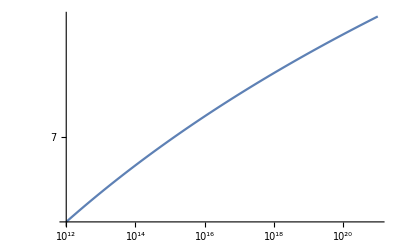

```mathematica
LogLogPlot[√(Log[x]*2/(2-EulerGamma)),{x,1*^12,1*^21}]
```

```mathematica
√(Log[1*^18]*2/(2-EulerGamma))//N
```

7.6329

```mathematica
(√3*δe*ℏ)/(√2*ge*wn*(z11+z22))*√(Log[1*^18]*2/(2-EulerGamma))/√2//.{ℏ-> 1/(2π),δe-> 316,ge-> 0.4975,z11-> 0.009617,z22-> 0.009883,wn-> 323}
```

106.096

```mathematica
2(ge wn (1/(√3) (-(z11+z22))-√(2/3)(√2 (z11+z22))))/(2 √2 δe)//Simplify
```

-(√(3/2) ge wn (z11+z22))/δe